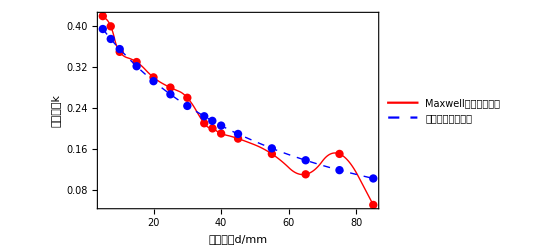

```mathematica
dist=Import["D:/Data/dist2.csv"];
dist2=Import["D:/Data/dist1.csv"];
p1=ListLinePlot[dist,InterpolationOrder->2,Mesh->Full,
PlotLegends->Placed[{"Maxwell仿真耦合系数"},{0.6,0.85}],
FrameLabel->{Style["线圈间距d/mm",Black],Style["耦合系数k",Black]},

Frame->True,
PlotStyle->{Red,Thick}];
p2=ListLinePlot[dist2,InterpolationOrder->2,Mesh->Full,
PlotLegends->Placed[{"实际测量耦合系数"},{0.6,0.75}],
Frame->True,
PlotStyle->{Blue,Dashed,Thick}];

Show[p1,p2,PlotRange->All]
```